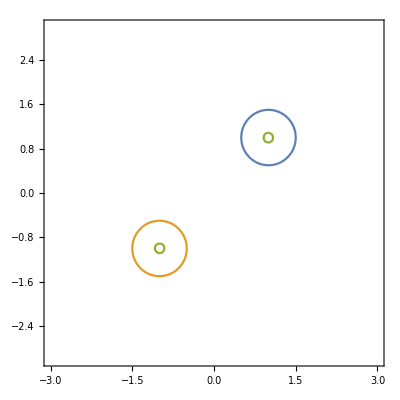

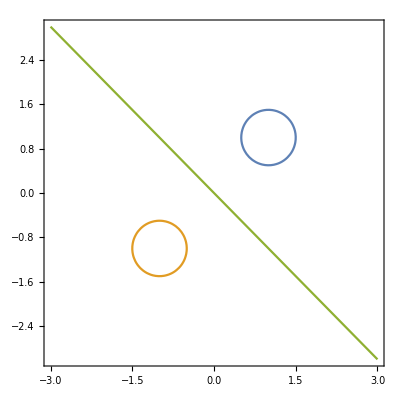

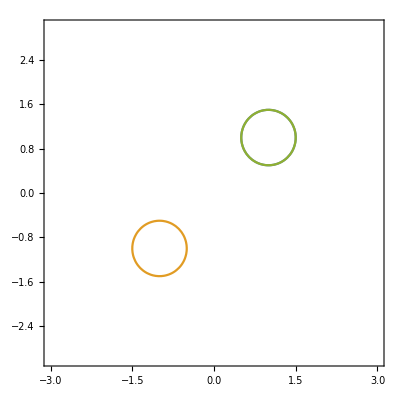

```mathematica
L={(x-1)^2+(y-1)^2,(x+1)^2+(y+1)^2,(x+1)^2+(y-1)^2};
R={1/4,1/4,1/4};
ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
L[[1]]L[[2]]==R[[1]]R[[2]]},
{x,-3,3},{y,-3,3}]
ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
L[[1]]R[[2]]==R[[1]]L[[2]]},
{x,-3,3},{y,-3,3}]
ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
(L[[1]]-R[[1]])L[[2]]==0},
{x,-3,3},{y,-3,3}]
Manipulate[ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
(L[[1]]-(1-m)R[[1]])(L[[2]]-(1-m) R[[2]])==m^2 R[[1]]R[[2]]},
{x,-3,3},{y,-3,3},
PlotLabel->"Full Blend"],
{{m,0},-5,5}]
Manipulate[ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
(L[[1]]-(1-m)R[[1]])(L[[2]])==m R[[1]]R[[2]]},
{x,-3,3},{y,-3,3},
PlotLabel->"Partial Blend"],
{{m,1},-5,5}]
Manipulate[ContourPlot[
{L[[1]]-R[[1]]==0,
L[[2]]-R[[2]]==0,
L[[3]]-R[[3]]==0,
((1-m)(m+1))/1(L[[1]]-R[[1]])+((m)(m+1))/2 (L[[2]]-R[[2]])+((m)(m-1))/2 (L[[3]]-R[[3]])==0},
{x,-3,3},{y,-3,3},
PlotLabel->"Transition Blend",
PlotPoints->100],
{{m,0},-1,1}]
```